بخش اول

قسمت اول

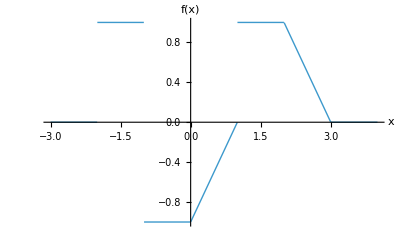

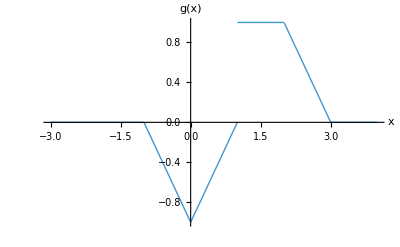

```mathematica
f[x_]:= UnitStep [x + 2 ] - 2 UnitStep[ x+1 ] + x*UnitStep[x] - (x - 1)*UnitStep[x-1] + UnitStep[x-1] - (x-2)*UnitStep[x-2] + (x-3)*UnitStep[x-3] 
g[x_] := -(x+1)*UnitStep[x+ 1] + 2x*UnitStep[x] - (x-1)*UnitStep[x-1] + UnitStep[x-1] - (x-2)*UnitStep[x - 2] + (x-3)*UnitStep[x - 3] 
Plot [f[x],{x , -3 , 4 }  ,PlotStyle->Thick, AxesLabel-> { "x","f(x)" }] 
Plot [g[x],{x , -3 , 4 }  , PlotStyle->Thick,AxesLabel-> { "x","g(x)" }]
```

Piecewise[{{1, 1≤x≤2}, {-1+Abs[x], Abs[x]<1}, {3-x, 2≤x≤3}, {0, True}}]

Piecewise[{{1, 1≤Abs[x]≤2}, {3-x, 2≤x≤3}, {-1, -1≤x≤0}, {-1+x, 0≤x<1}, {0, True}}]

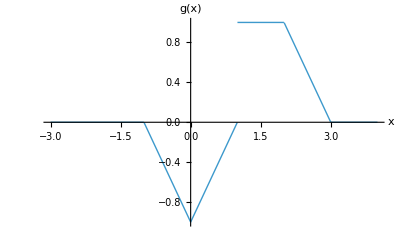

-Graphics-

```mathematica
g[x_] = Piecewise[{{1 , 1  <= x<= 2} , {Abs[x] - 1 , Abs[x] < 1} , { -x+3 , 2<= x <= 3}} , 0]
f[x_] = Piecewise[{{1 , 1  <= Abs[x]<= 2},{ -x+3 , 2<= x <= 3} , { -1 , -1 <= x <= 0} , { x - 1  , 0 <=x <1 }} , 0 ]
Plot [g[x],{x , -3 , 4 }  ,PlotStyle->Thick, AxesLabel-> { "x","g(x)" }] 
Plot [f[x],{x , -3 , 4 }  ,PlotStyle->Thick, AxesLabel-> { "x","f(x)" }]
```

قسمت دوم

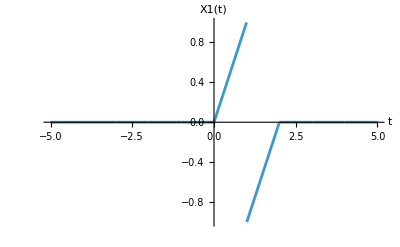

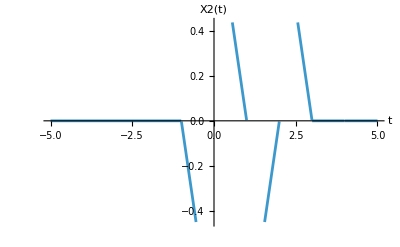

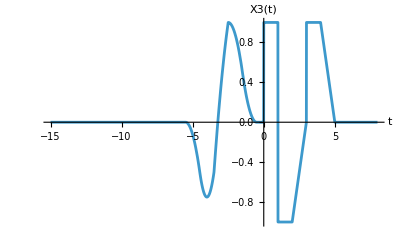

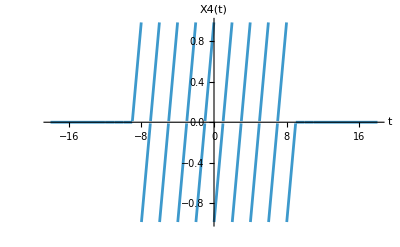

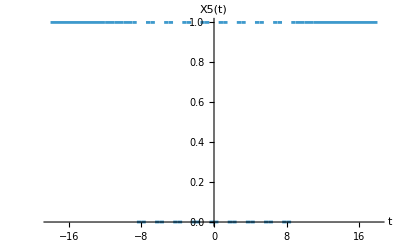

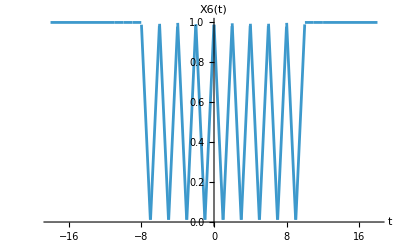

```mathematica
Plot[g[x-1] f[-x] , {x , - 5 , 5} , AxesStyle->Thick , AxesLabel-> {"t" , "X1(t)"}]
Plot[g[x] f[x-1] , {x , - 5 , 5} , AxesStyle->Thick , AxesLabel-> {"t" , "X2(t)"}]
X3[x_] := Piecewise[{{Convolve[g[t+4],UnitBox[t] , t , x] , x < 0 } , {f[x-2] , x >= 0}} , 0] 
Plot[X3[x] , {x , - 15 , 8 } , AxesStyle->Thick , AxesLabel-> {"t" , "X3(t)"}]
Plot[∑_(k=-4)^4 g[x-2k]* f[-1-x+2k], {x , - 18 , 18 }, AxesStyle->Thick  , AxesLabel->{"t" , "X4(t)"}]
Plot[UnitBox[∑_(k=-4)^4 g[x-2k]* f[-1-x+2k]], {x , - 18 , 18 }, AxesStyle->Thick  , AxesLabel->{"t" , "X5(t)"}]
Plot[UnitTriangle[∑_(k=-4)^4 g[(x-1)-2k]* f[-1-(x-1)+2k]], {x , - 18 , 18 }, AxesStyle->Thick  , AxesLabel->{"t" , "X6(t)"}]
```

بخش دوم

قسمت اول

```mathematica
X1[t_] := A ⅇ^(-a t) UnitStep[t]
X2[t_] := A Sin[ 2 Pi t / T0 + fi  ]
X3[t_] := 1 / ( Abs[t]^3 + 1 )
X4[t_] := UnitStep[ t - 4 ] / t^(1/4)
X5[t_] := ⅇ^(-3 t)Cos[Pi * t / 2 ] UnitStep[t]
X[t_] := (1−UnitBox [Sinc[Pi t  / 4]]) Sinc[Pi t  / 4]
X6[t_] := ∑_(k=-∞)^∞ X[t - 6 k ]
 X1_energy =  Integrate[X1[t]^2 , {t , 0 , Infinity} , Assumptions-> a > 0]
```

A^2/(2 a)

```mathematica
X1_power =  Limit[ Integrate[ X1[t] ^ 2  , {t , 0 , T} ] / (2  T ),  T -> Infinity , Assumptions-> a > 0]
```

0

```mathematica
X2_energy = Limit [Integrate[X2[t]^2 , {t , 0, T0 } ] * k , k-> Infinity]
```

```mathematica
∞
```

```mathematica
X2_power = Integrate[ X2[t] ^ 2  , {t , 0 , T0} ] / T0
```

A^2/2

```mathematica
X3_energy =  Integrate[X3[t]^2 , {t , -Infinity, Infinity}]
```

(8 π)/(9 √3)

```mathematica
X3_power = Limit[X3_energy / (2 T) , T -> Infinity]
```

0

```mathematica
X4_energy =  Integrate[1 / Sqrt[t] , {t , 4, Infinity}]
```

Integrate::idiv: Integral of 1/(√t) does not converge on {4,∞}.

```mathematica
∫_4^∞ 1/(√t)ⅆt = ∞
```

```mathematica
X4_power = Limit[Integrate[1 / Sqrt[t] , {t , 4, T}] / (2 T) , T -> Infinity]
```

0

```mathematica
X5_energy =  Integrate[X5[t]^2 , {t ,0, Infinity}]
```

1/12+3/(36+π^2)

```mathematica
X5_power = Limit[X5_energy / (2 T) , T -> Infinity]
```

0

```mathematica
X_energy = N [Integrate[X[t]^2 , {t , -Infinity, Infinity}]]
```

```mathematica
3.363799590045463 * ∞ -> X6 has Infinite energy
```

```mathematica
Plot[X[t] , {t , -6, 6}]
```

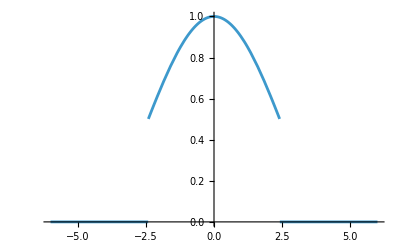
```mathematica
-Graphics- -> X6 is priodic Function
```

```mathematica
X6_power = N [Integrate[X[t]^2 , {t , -3, 3}]] / 6
```

0.560633

قسمت دوم
نکته اول

```mathematica
X3_energy =  Integrate[X3[t]^2 , {t , -Infinity, Infinity}]
```

(8 π)/(9 √3)

```mathematica
Integrate[X3[t]^2 , {t , -Infinity, 0}] +  Integrate[X3[t]^2 , {t , 0, Infinity}]
```

(8 π)/(9 √3)

```mathematica
Limit[Integrate[((4 x^2 + 7x -2) / (x^2 + 1 ))^2  , {x , -T , T } ] / (2 T), T -> Infinity  ]
```

16

```mathematica
N[Limit[Integrate[((4 x^2 + 7x -2) / (x^2 + 1 ))^2  , {x , -T , -10 } ] / (T -10), T -> Infinity  ] + Integrate[((4 x^2 + 7x -2) / (x^2 + 1 ))^2  , {x , -10 , 10 } ] / 20+Limit[Integrate[((4 x^2 + 7x -2) / (x^2 + 1 ))^2  , {x , 10 , T } ] / (T -10), T -> Infinity  ]]
```

47.1265

نکته دوم

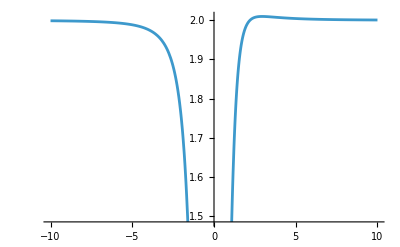

```mathematica
g[x_] := (10x^4  + 5x - 3)/(5x^4  + 4)
Plot[g[x] , {x , -10 , 10}]
```

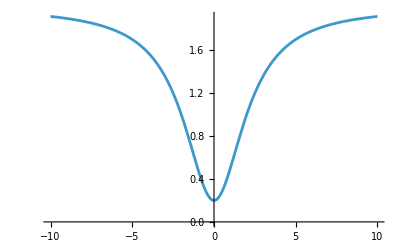

```mathematica
f[x_] := (2x^2 + 1) / (x^2 + 5)
Plot[f[x] , {x , -10 , 10}]
```

```mathematica
Limit[Integrate[(f[x])^2  , {x , -T , T } ] / (2 T), T -> Infinity  ]
```

4

```mathematica
Limit[Integrate[(g[x])^2  , {x , -T , T } ] / (2 T), T -> Infinity  ]
```

4

نکته سوم

```mathematica
Limit[Integrate[(f[x])^2  , {x , -T , T } ] / (2 T), T -> Infinity  ]
```

4

```mathematica
((Limit[f[x], x -> Infinity] )^2 +(Limit[f[x], x -> -Infinity] )^2)/2
```

4

بخش سوم

قسمت اول

```mathematica
Manipulate[Plot[{Cos[3t - k] +Sin[5t - k] ,Cos[3t] +Sin[5t]  } , {t  , - Pi , Pi}] , {k , 0 , 20}]
```

main period = 6.3

```mathematica
Manipulate[Plot[{Cos[Pi (t- k) / 5] Sin[Pi (t-k) /3] ,Cos[Pi t / 5] Sin[Pi t /3]  } , {t  , - 10 , 10}] , {k , 0 , 20}]
```

main period = 15

```mathematica
Manipulate[Plot[{ Sum[UnitStep[t -k- 2i]  UnitStep[2i - t +k+1 ] , {i , 0 , 50}] ,Sum[UnitStep[t - 2i]  UnitStep[2i - t +1] , {i , 0 , 50}]  } , {t  , -10, 20}] , {k , 0 , 20}]
```

```mathematica
Manipulate[Plot[{ Sum[UnitStep[t -k- 2i]  UnitStep[2i - t +k+1 ] , {i , -50 , 50}] ,Sum[UnitStep[t - 2i]  UnitStep[2i - t +1] , {i , -50, 50}]  } , {t  , -5, 5}] , {k , 0 , 20}]
```

main period = 2

```mathematica
Manipulate[Plot[{Sin[t - k]UnitStep[t - k],Sin[t]UnitStep[t]} , {t  , - 10 , 10}] , {k , 0 , 20}]
```

```mathematica
Manipulate[Plot[{Cos[t - k]UnitStep[t - k],Cos[t]UnitStep[t]} , {t  , - 10 , 10}] , {k , 0 , 20}]
```

```mathematica
Manipulate[Plot[{ Sum[UnitTriangle[t -k- 3/5i], {i , -50 , 50}] ,Sum[UnitTriangle[t- 3/5i] , {i , -50, 50}]  } , {t  , -3, 3}] , {k , 0 , 20}]
```

main period = 0.6

```mathematica
Manipulate[Plot[{ Sum[E^-(Abs[t -k- 2i]), {i , -50 , 50}] ,Sum[E^-(Abs[t - 2i]) , {i , -50, 50}]  } , {t  , -5, 5}] , {k , 0 , 20}]
```

main period = 2

قسمت دوم

```mathematica
Manipulate[Plot[{Cos[3t - k] +Sin[5t - k]+ Cos[Pi (t- k) / 5] Sin[Pi (t-k) /3] ,Cos[3t] +Sin[5t]+Cos[Pi (t) / 5] Sin[Pi (t) /3]  } , {t  , - 10, 10}] , {k , 0 , 200}]
```

بخش چهارم

```mathematica
Integrate[(E^(-3t) Cos[Pi t /2] + UnitTriangle[t/2 - 1]) DiracDelta'[t - 0.5],{t ,-100 , 100}]
```

0.221166

```mathematica
Integrate[(t^2 + 2)DiracDelta''[t+1] + (E^(-Abs[t]) + t^2 + 2 ) DiracDelta[E^(-Abs[t]) + t^2 + 1],{t ,-100 , 100}]
```

2

```mathematica
Integrate[(t^2 + 1) (DiracDelta'[2t - 6] + DiracDelta[t^2 - 1]),{t ,0 , 100}]
```

-1/2

بخش پنجم

```mathematica
Animate[Plot[Sinc[t/e]^2/e,{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True]
Limit[Integrate[Sinc[t/e]^2/e , {t , -Sqrt[e] , Sqrt[e]}] , e-> 0]
Export[  "sinc.gif",Animate[Plot[Sinc[t/e]^2/e,{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True] , "AnimationRepetition" -> Infinity]
```

Indeterminate

sinc.gif

```mathematica
Animate[Plot[UnitBox[t/(4e)]/(4e),{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True]
Limit[Integrate[UnitBox[t/(4e)]/(4e) , {t , -2e , 2e}] , e-> 0]
Export[  "unitbox.gif",Animate[Plot[UnitBox[t/(4e)]/(4e),{t,-1,1},Exclusions->None],{e,1,-0.2,0.001},AnimationRunning->True] , "AnimationRepetition" -> Infinity]
```

1

unitbox.gif

```mathematica
Animate[Plot[UnitTriangle[t/e]/e,{t,-1,1},Exclusions->None],{e,1,-0.2,0.001},AnimationRunning->True]
Limit[Integrate[UnitTriangle[t/e]/e , {t , -e , e}] , e-> 0]
Export[  "unitteringle.gif",Animate[Plot[UnitTriangle[t/e]/e,{t,-1,1},Exclusions->None],{e,1,-0.2,0.001},AnimationRunning->True] , "AnimationRepetition" -> Infinity]
```

1

unitteringle.gif

```mathematica
Animate[Plot[(E^(-t/e) UnitStep[t])/e,{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True]
Limit[Integrate[(E^(-t/e) UnitStep[t])/e , {t , 0, Sqrt[e]}] , e-> 0]
Export[  "exponential.gif",Animate[Plot[(E^(-t/e) UnitStep[t])/e,{t,-1,1},Exclusions->None],{e,1,-0.2,0.001},AnimationRunning->True] , "AnimationRepetition" -> Infinity]
```

Indeterminate

exponential.gif

```mathematica
Animate[Plot[Sin[t / Abs[e]]/(Pi t),{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True]
Export[  "X5.gif",Animate[Plot[Sin[t / Abs[e]]/(Pi t),{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True] , "AnimationRepetition" -> Infinity]
```

X5.gif

```mathematica
Animate[Plot[Abs[e]/(Pi (e^2 + t^2)),{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True]
Export[  "X6.gif",Animate[Plot[Abs[e]/(Pi (e^2 + t^2)),{t,-1,1},Exclusions->None],{e,1,-0.1,0.001},AnimationRunning->True], "AnimationRepetition" -> Infinity]
```

X6.gif